```mathematica
(* 
        CALCULATE EFFECTIVE HAMILTOIAN IN *ONE* FUNCTION
*)
```

```mathematica
Quit[]
```

```mathematica
(* INITIALIZATION *)
```

```mathematica
(* INPUT 1 *)

(* Generic Hamiltonian *)
H[t_]=H1/4 (Cos[phi]sx+sx Cos[2 t ww+phi]+Sin[phi]sy-sy Sin[2 t ww+phi])+(Delta/2)sz(*/.phi->0*)/.Delta->0;

(* set maximum order of 1/ww, and set up list of coefficients (for sTrim),  in case of taylor == True 
the highest "reasonable" max is 5 *)
(* we have the result for max = 8 below. *)
max=8;

(* coeffs1 = time-dependent coefficients of original Hamiltonian [no derivatives] *)
coeffs1={{H1,1}(*,{H2,1}*)};

(*offResonant = True or False*)
offResonant=False;

(*taylor Expansion = True or False*)
taylor=False;

(* how much output should be written *)
verbose=False;
verboseLight=False;
(*verbose=True;
verboseLight=True;*)
(*t0=0;*)


(* --------------- *)
(*  LOAD SCRIPT  *)
(* --------------- *)

myDir=NotebookDirectory[];
nb1=NotebookOpen[myDir <> "/scripts/Magnus_script_precalculated.nb"];
SelectionMove[nb1,All,Notebook];
SelectionEvaluate[nb1];
```

```mathematica
t0=0;
```

```mathematica
NotebookSave[nb1];
NotebookClose[nb1];

(* contains NCAlgebra initialization and MagnusM and MAgnusM2 *)
nb2=NotebookOpen[myDir <> "/scripts/Magnus_scriptEffH.nb"];
SelectionMove[nb2,All,Notebook];
SelectionEvaluate[nb2];
```

```mathematica
(* INPUT *)
(* coefficients="simple" 
in case there are at most two coefficients, which we call H1 and H2 *)
coefficients="simple";
coefficients="NotSoSimple";
If[coefficients=="simple",
updateCoeffsSimple,
(*otherwise determine the coefficients laboriously*)
updateCoeffs;
];
myCList
```

{{{H1},1},{{H1^2},2},{{H1^3},3},{{H1^4},4},{{H1^5},5},{{H1^6},6},{{H1^7},7},{{H1^8},8},{{H1^9},9}}

```mathematica
NotebookSave[nb2];
NotebookClose[nb2];
```

```mathematica
(*$RecursionLimit=5000*)
```

### Seventh order

```mathematica
AbsoluteTiming[M[H[t],max,True]]
```

```mathematica
(* for final integral, use FastIntegral *)
(*experimental notebook.*)
(**tryout, we have changed //S -> Expand**)
AbsoluteTiming[M[H[t],max]]
```

[in sGet]  Begin calculating ΩΩ_k/Omega_k of order k = 1, at date and time {2019,4,30,12,22,43.04532}

[in M[HH, max]]  i = 1

[in sGet]  Begin calculating ΩΩ_k/Omega_k of order k = 2, at date and time {2019,4,30,12,22,46.527569}

[in M[HH, max]]  i = 2

[in sGet]  Begin calculating ΩΩ_k/Omega_k of order k = 3, at date and time {2019,4,30,12,22,53.788922}

[in M[HH, max]]  i = 3

[in sGet]  Begin calculating ΩΩ_k/Omega_k of order k = 4, at date and time {2019,4,30,12,23,24.353094}

[in M[HH, max]]  i = 4

[in sGet]  Begin calculating ΩΩ_k/Omega_k of order k = 5, at date and time {2019,4,30,12,23,58.876321}

[in M[HH, max]]  i = 5

[in sGet]  Begin calculating ΩΩ_k/Omega_k of order k = 6, at date and time {2019,4,30,12,28,8.865075}

[in M[HH, max]]  i = 6

[in sGet]  Begin calculating ΩΩ_k/Omega_k of order k = 7, at date and time {2019,4,30,12,32,33.670265}

[in M[HH, max]]  i = 7

[in sGet]  Begin calculating ΩΩ_k/Omega_k of order k = 8, at date and time {2019,4,30,13,21,39.062376}

[in M[HH, max]]  i = 8

[in sGet]  Begin calculating ΩΩ_k/Omega_k of order k = 9, at date and time {2019,4,30,14,1,56.8018}

Now:  final integral for Omega[t0]

{7977.91,1/(173946175488 ww^8)H1 (-487296 H1^7 sz ww-1990656 H1^5 sz ww^3+84934656 H1^3 sz ww^5+5435817984 H1 sz ww^7-1296 sx (185 H1^8+4352 H1^6 ww^2+73728 H1^4 ww^4+1048576 H1^2 ww^6-33554432 ww^8) Cos[phi]+20736 H1 sz ww (47 H1^6+192 H1^4 ww^2-8192 H1^2 ww^4-524288 ww^6) Cos[2 phi]-34704 H1^8 sx Cos[3 phi]+580608 H1^6 sx ww^2 Cos[3 phi]+26542080 H1^4 sx ww^4 Cos[3 phi]+679477248 H1^2 sx ww^6 Cos[3 phi]-419328 H1^7 sz ww Cos[4 phi]-13271040 H1^5 sz ww^3 Cos[4 phi]-254803968 H1^3 sz ww^5 Cos[4 phi]+11816 H1^8 sx Cos[5 phi]+322560 H1^6 sx ww^2 Cos[5 phi]+5308416 H1^4 sx ww^4 Cos[5 phi]-147840 H1^7 sz ww Cos[6 phi]-2211840 H1^5 sz ww^3 Cos[6 phi]+1645 H1^8 sx Cos[7 phi]+23040 H1^6 sx ww^2 Cos[7 phi]-10080 H1^7 sz ww Cos[8 phi]+63 H1^8 sx Cos[9 phi]-239760 H1^8 sy Sin[phi]-5640192 H1^6 sy ww^2 Sin[phi]-95551488 H1^4 sy ww^4 Sin[phi]-1358954496 H1^2 sy ww^6 Sin[phi]+43486543872 sy ww^8 Sin[phi]-104112 H1^8 sy Sin[3 phi]+1741824 H1^6 sy ww^2 Sin[3 phi]+79626240 H1^4 sy ww^4 Sin[3 phi]+2038431744 H1^2 sy ww^6 Sin[3 phi]+59080 H1^8 sy Sin[5 phi]+1612800 H1^6 sy ww^2 Sin[5 phi]+26542080 H1^4 sy ww^4 Sin[5 phi]+11515 H1^8 sy Sin[7 phi]+161280 H1^6 sy ww^2 Sin[7 phi]+567 H1^8 sy Sin[9 phi])}

#### Result up to order 1/ww^8

```mathematica
HEff8Phi[phi_]=1/(173946175488 ww^8)H1 (-487296 H1^7 sz ww-1990656 H1^5 sz ww^3+84934656 H1^3 sz ww^5+5435817984 H1 sz ww^7-1296 sx (185 H1^8+4352 H1^6 ww^2+73728 H1^4 ww^4+1048576 H1^2 ww^6-33554432 ww^8) Cos[phi]+20736 H1 sz ww (47 H1^6+192 H1^4 ww^2-8192 H1^2 ww^4-524288 ww^6) Cos[2 phi]-34704 H1^8 sx Cos[3 phi]+580608 H1^6 sx ww^2 Cos[3 phi]+26542080 H1^4 sx ww^4 Cos[3 phi]+679477248 H1^2 sx ww^6 Cos[3 phi]-419328 H1^7 sz ww Cos[4 phi]-13271040 H1^5 sz ww^3 Cos[4 phi]-254803968 H1^3 sz ww^5 Cos[4 phi]+11816 H1^8 sx Cos[5 phi]+322560 H1^6 sx ww^2 Cos[5 phi]+5308416 H1^4 sx ww^4 Cos[5 phi]-147840 H1^7 sz ww Cos[6 phi]-2211840 H1^5 sz ww^3 Cos[6 phi]+1645 H1^8 sx Cos[7 phi]+23040 H1^6 sx ww^2 Cos[7 phi]-10080 H1^7 sz ww Cos[8 phi]+63 H1^8 sx Cos[9 phi]-239760 H1^8 sy Sin[phi]-5640192 H1^6 sy ww^2 Sin[phi]-95551488 H1^4 sy ww^4 Sin[phi]-1358954496 H1^2 sy ww^6 Sin[phi]+43486543872 sy ww^8 Sin[phi]-104112 H1^8 sy Sin[3 phi]+1741824 H1^6 sy ww^2 Sin[3 phi]+79626240 H1^4 sy ww^4 Sin[3 phi]+2038431744 H1^2 sy ww^6 Sin[3 phi]+59080 H1^8 sy Sin[5 phi]+1612800 H1^6 sy ww^2 Sin[5 phi]+26542080 H1^4 sy ww^4 Sin[5 phi]+11515 H1^8 sy Sin[7 phi]+161280 H1^6 sy ww^2 Sin[7 phi]+567 H1^8 sy Sin[9 phi]);
```

```mathematica
NotebookSave[]
```

```mathematica
Print["I am curious as to how the ``real Rabi frequency'' omegaRR (which is determined by the absolute value squared of the Hamiltonian) for constant driving depends on phi.  Numerical calculations in HEff_constH1_phi-Average.nb suggest that omegaRR is independent of phi --- because the numerical solution commensurability seems to be 'unchanged' when changing phi."]
```

#### Write HEff8 as a vector (HEff8 = n \cdot \sigma) and compute its absolute value

```mathematica
vectorize={sx->{1,0,0},sy->{0,1,0},sz->{0,0,1}};
```

```mathematica
HEff8V=HEff8Phi[phi]/.vectorize;
```

#### HEff8 as a vector (HEff8 = n \cdot \sigma) and compute its absolute value

```mathematica
maxOrder=1;
HEffVX=HEff8V/.ww->1/xx;
HEff8VV[H1_,phi_]=(Series[HEffVX2,{xx,0,maxOrder}]/.vectorize//Normal//S)/.xx->1
```

{1/4 H1 Cos[phi],1/4 H1 Sin[phi],1/32 H1^2 (1-2 Cos[2 phi])}

```mathematica
abs[H1_,phi_]:=Sqrt[Sum[(HEff8VV[H1,phi][[i]])^2,{i,1,3}]];
```

```mathematica
Manipulate[Plot[4abs[H1,phi],{phi,0,2Pi},PlotRange->{0,1}],{H1,0.00001,0.99}]
```

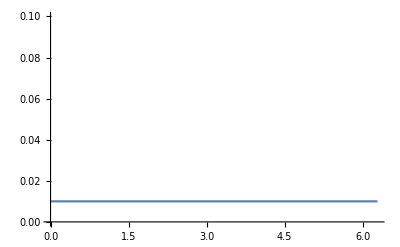

```mathematica
Plot[4abs[.01,phi],{phi,0,2Pi},PlotRange->{0,0.1}]
```